```mathematica
DSolve[α''[x] + ρ Sin[α[x]]==0,α[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{α[x]→-2 JacobiAmplitude[1/2 √((2 ρ+C[1]) (x+C[2])^2),(4 ρ)/(2 ρ+C[1])]},{α[x]→2 JacobiAmplitude[1/2 √((2 ρ+C[1]) (x+C[2])^2),(4 ρ)/(2 ρ+C[1])]}}

```mathematica
JacobiAmplitude[x/2 √(2 ρ+C[1]),(4 ρ)/(2 ρ+C[1])] + O[x]^2
```

1/2 √(2 ρ+C[1]) x+O[x]^2

```mathematica
JacobiAmplitude[x/2 √(2 ρ1+C[1]),(4 ρ1)/(2 ρ1+C[1])]-JacobiAmplitude[x/2 √(2 ρ2+C[2]),(4 ρ2)/(2 ρ2+C[2])] + O[x]^2
```

1/2 (√(2 ρ1+C[1])-√(2 ρ2+C[2])) x+O[x]^2

```mathematica
sub ={C[1] -> a^2 - 2 ρ1,C[2] -> a^2 - 2 ρ2}
```

{C[1]→a^2-2 ρ1,C[2]→a^2-2 ρ2}

```mathematica
JacobiAmplitude[(x-ξ2)/2 √(2 ρ1+C[1]),(4 ρ1)/(2 ρ1+C[1])]/.sub
```

JacobiAmplitude[1/2 √(a^2) (x-ξ2),(4 ρ1)/a^2]

```mathematica
JacobiAmplitude[(x-ξ2)/2 √(2 ρ2+C[2]),(4 ρ2)/(2 ρ2+C[2])]/.sub
```

JacobiAmplitude[1/2 √(a^2) (x-ξ2),(4 ρ2)/a^2]

```mathematica
F[a_,r_,ξ_] := JacobiAmplitude[ξ/2a,r/(a^2 ξ)]-JacobiAmplitude[(1-ξ)/2 a,-r/(a^2(1-ξ))]
```

```mathematica
FindRoot[F[a,1000,0.1],{a,-10,-0.1}]
```

{a→-2.88328}

```mathematica
FindRoot[F[0.0001,r,0.55],{r,40}]
```

{r→4.79313}

```mathematica
r=.;
```

```mathematica
4Integrate[D[JacobiAmplitude[(x-ξ)/2a,r/(a^2 ξ)],x]^2,{x,0,ξ}]
```

2 a JacobiEpsilon[(a ξ)/2,r/(a^2 ξ)]

```mathematica
4Integrate[D[JacobiAmplitude[(x-ξ)/2a,-r/(a^2 (1-ξ))],x]^2,{x,ξ,1}]
```

2 a JacobiEpsilon[1/2 a (1-ξ),r/(a^2 (-1+ξ))]

```mathematica
2 a (JacobiEpsilon[(a ξ)/2,r/(a^2 ξ)] + JacobiEpsilon[1/2 a (1-ξ),r/(a^2 (-1+ξ))])
```

2 a (JacobiEpsilon[1/2 a (1-ξ),r/(a^2 (-1+ξ))]+JacobiEpsilon[(a ξ)/2,r/(a^2 ξ)])

```mathematica
Integrate[Exp[I 2JacobiAmplitude[(x-ξ)/2a,r/(a^2 ξ)]],{x,0,ξ}]
```

∫_0^ξ ⅇ^(2 ⅈ JacobiAmplitude[1/2 a (x-ξ),r/(a^2 ξ)])ⅆx

```mathematica
2D[JacobiAmplitude[(x-ξ)/2a,r/(a^2 ξ)],x]/.x->0
```

a JacobiDN[(a ξ)/2,r/(a^2 ξ)]

```mathematica
2D[JacobiAmplitude[(x-ξ)/2a,r/(a^2 ξ)],x]/.x->ξ
```

a

```mathematica
a^2 JacobiDN[(a ξ)/2,r/(a^2 ξ)]
```

a^2 JacobiDN[(a ξ)/2,r/(a^2 ξ)]

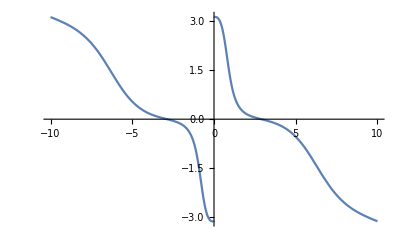

```mathematica
Plot[F[a,1000,0.1],{a,-10,10}]
```

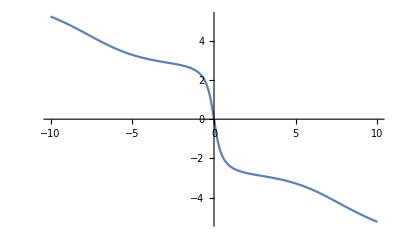

```mathematica
Plot[F[a,100,0.1],{a,-10,10}]
```

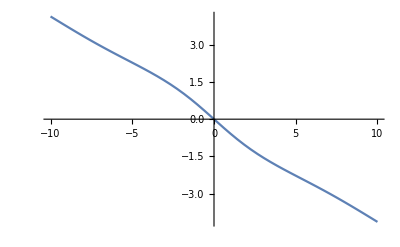

```mathematica
Plot[F[a,10,0.1],{a,-10,10}]
```

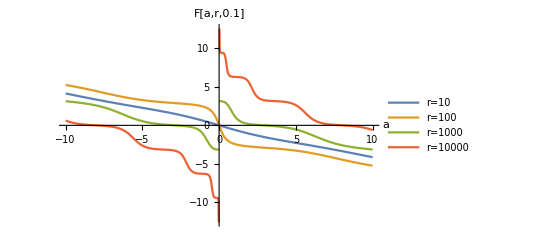

λ_(1,2)=={r/Δ,r/(-1+Δ)}

```mathematica
Plot[{F[a,10,0.1],F[a,100,0.1],F[a,1000,0.1],F[a,10000,0.1]},{a,-10,10},
PlotLabel->"F[a,r,0.1]",AxesLabel->{"a",None},
PlotLegends->{"r=10","r=100","r=1000","r=10000"}]
```

```mathematica
(*The solution matching with first derivative at $\xi = \xi_2$ reads (up to irrelevant common normalization factor)*)
```

```mathematica
SpectrumEq[d_,  ω_, r_]:=
Block[{K1, K2, F1, F2,DF1, DF2, B, sol, x},
K1 =Sqrt[r/d + ω];
K2 =Sqrt[r/(d-1) + ω];
(* x = ξ- ξ_2*);
F1 = Cos[K1 x] + B Sin[K1 x]/K1;
F2 = Cos[K2 x] + B Sin[K2 x]/K2;
DF1= D[F1,x];
DF2 = D[F2,x];
sol =Solve[{ (DF1/.x->-d)== (DF2/.x->1-d)}, B][[1]];
Print[FullSimplify[B/.sol]];
FullSimplify[((F1/.x->-d)- (F2/.x->1-d))/.sol]
]
```

```mathematica
Eq=Numerator[SpectrumEq[Δ,  ω, r]]
```

(√(r/(-1+Δ)+ω) Sin[(1-Δ) √(r/(-1+Δ)+ω)]+√(r/Δ+ω) Sin[Δ √(r/Δ+ω)])/(Cos[(-1+Δ) √(r/(-1+Δ)+ω)]-Cos[Δ √(r/Δ+ω)])

-2 √Δ (r+(-1+Δ) ω) √(r+Δ ω)+2 √Δ (r+(-1+Δ) ω) √(r+Δ ω) Cos[(-1+Δ) √(r/(-1+Δ)+ω)] Cos[Δ √(r/Δ+ω)]+√(r/(-1+Δ)+ω) (r (-1+2 Δ)+2 (-1+Δ) Δ ω) Sin[(-1+Δ) √(r/(-1+Δ)+ω)] Sin[√Δ √(r+Δ ω)]

```mathematica
gg[r_,Δ_] :=Evaluate[Numerator[FullSimplify[(Eq/.ω->0)/(r Sqrt[Δ r]),{1/2 < Δ <1, r >0}]]/r^2];
```

```mathematica
gg[r,Δ]
```

(-2+2 Cos[√(r (-1+Δ))] Cos[√(r Δ)]+((-1+2 Δ) Sin[√(r (-1+Δ))] Sin[√(r Δ)])/(√((-1+Δ) Δ)))/r^2

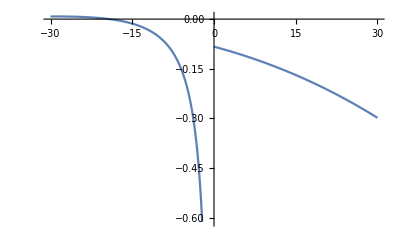

```mathematica
Plot[gg[r,0.1],{r,-30,30}]
```

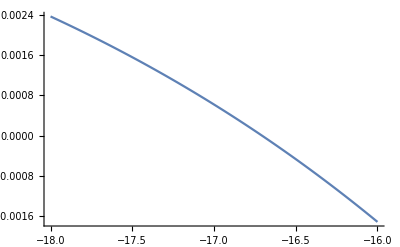

```mathematica
Plot[gg[r,0.01],{r,-18,-16}]
```

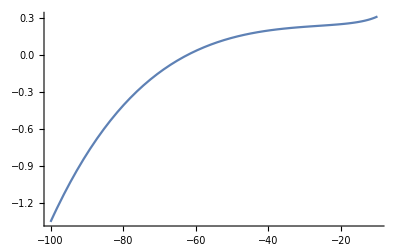

```mathematica
Plot[gg[r,0.9],{r,-100,-10}]
```

```mathematica
Action[d_,  r_]:=
Block[{K1, K2, F1, F2,DF1, DF2, B, sol, x},
K1 =Sqrt[r/d ];
K2 =Sqrt[r/(d-1)];
(* x = ξ- ξ_2*);
F1 = Cos[K1 x] + B Sin[K1 x]/K1;
F2 = Cos[K2 x] + B Sin[K2 x]/K2;
DF1= D[F1,x];
DF2 = D[F2,x];
sol =Solve[{ (DF1/.x->-d)== (DF2/.x->1-d)}, B][[1]];
FullSimplify[Integrate[(DF1/.sol)^2,{x,-d,0}] +Integrate[(DF2/.sol)^2,{x, 0,1-d}]]
]
```

```mathematica
action[r_, Δ_] :=Evaluate[Action[Δ,  r]];
```

```mathematica
action[r, Δ]
```

(√r (-8 √r √(-1+Δ) √Δ Cos[√r (√(-1+Δ)-√Δ)]+8 √r √(-1+Δ) √Δ Cos[√r (√(-1+Δ)+√Δ)]+4 √r (-1+2 Δ-Δ Cos[2 √r √(-1+Δ)]-(-1+Δ) Cos[2 √r √Δ])-8 √(-1+Δ) Δ Sin[√r (√(-1+Δ)-√Δ)]-√(-1+Δ) Sin[2 √r (√(-1+Δ)-√Δ)]+4 √(-1+Δ) Δ Sin[2 √r (√(-1+Δ)-√Δ)]-8 √(-1+Δ) Δ Sin[√r (√(-1+Δ)+√Δ)]-√(-1+Δ) Sin[2 √r (√(-1+Δ)+√Δ)]+4 √(-1+Δ) Δ Sin[2 √r (√(-1+Δ)+√Δ)]+2 √(-1+Δ) Sin[2 √r √(-1+Δ)]+√Δ (-8 (-1+Δ) Sin[√r (√(-1+Δ)-√Δ)]+(-3+4 Δ) Sin[2 √r (√(-1+Δ)-√Δ)]+8 (-1+Δ) Sin[√r (√(-1+Δ)+√Δ)]+(3-4 Δ) Sin[2 √r (√(-1+Δ)+√Δ)]+2 Sin[2 √r √Δ])))/(16 (-1+Δ) Δ (Cos[√r √(-1+Δ)]-Cos[√r √Δ])^2)

```mathematica
r/.FindRoot[gg[r,0.51],{r, -16.7}][[1]]
```

-46.0098+0. ⅈ

```mathematica
r/.FindRoot[gg[r,0.5],{r, 45}][[1]]
```

44.7466+0. ⅈ

```mathematica
r0data = Block[{data={}, delta = 0.001, r0 = -16.7},
d = delta;
While[d < 0.98,
r0 =Re[ r/.FindRoot[gg[r,d],{r, r0}][[1]]];
AppendTo[data,{d,r0}];
d += delta;
];
data
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
r0data[[;;10]]
```

{{0.001,-16.4873},{0.002,-16.5113},{0.003,-16.5353},{0.004,-16.5593},{0.005,-16.5835},{0.006,-16.6076},{0.007,-16.6319},{0.008,-16.6562},{0.009,-16.6806},{0.01,-16.705}}

```mathematica
{{0.001,-16.487313899806264},{0.002,-16.51125570734658},{0.003,-16.535259097117237},{0.004,-16.559324281715995},{0.005,-16.583451474624262},{0.006,-16.60764089021142},{0.007,-16.63189274373895},{0.008,-16.656207251364794},{0.009000000000000001,-16.680584630147585},{0.010000000000000002,-16.705025098050992}}
```

{{0.001,-16.4873},{0.002,-16.5113},{0.003,-16.5353},{0.004,-16.5593},{0.005,-16.5835},{0.006,-16.6076},{0.007,-16.6319},{0.008,-16.6562},{0.009,-16.6806},{0.01,-16.705}}

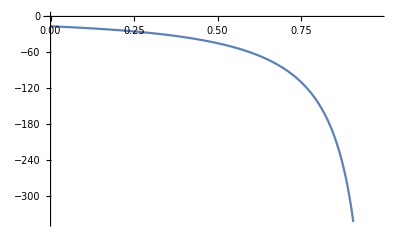

```mathematica
ListLinePlot[r0data]
```

```mathematica
r1data = Block[{data={}, d=0.5,delta = 0.001, r0 =-48 delta-(1536 delta^3)/7},
d += delta;
While[d < 0.96,
r0 = Re[ r/.FindRoot[gg[r,d],{r, r0}][[1]]];
AppendTo[data,{d,r0}];
d += delta;
];
data
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
r1data[[-50;;-10]]
```

{{0.91,-71.2247},{0.911,-72.2258},{0.912,-73.2508},{0.913,-74.3007},{0.914,-75.3763},{0.915,-76.4787},{0.916,-77.6086},{0.917,-78.7673},{0.918,-79.9557},{0.919,-81.175},{0.92,-82.4264},{0.921,-83.7111},{0.922,-85.0305},{0.923,-86.386},{0.924,-87.7789},{0.925,-89.2109},{0.926,-90.6836},{0.927,-92.1987},{0.928,-93.758},{0.929,-95.3633},{0.93,-97.0169},{0.931,-98.7207},{0.932,-100.477},{0.933,-102.288},{0.934,-104.157},{0.935,-106.087},{0.936,-108.079},{0.937,-110.137},{0.938,-112.265},{0.939,-114.467},{0.94,-116.744},{0.941,-119.103},{0.942,-121.546},{0.943,-124.08},{0.944,-126.707},{0.945,-129.435},{0.946,-132.267},{0.947,-135.212},{0.948,-138.274},{0.949,-141.462},{0.95,-144.782}}

```mathematica
r1data[[;;10]]
```

{{0.501,-0.0480002},{0.502,-0.0960018},{0.503,-0.144006},{0.504,-0.192014},{0.505,-0.240027},{0.506,-0.288047},{0.507,-0.336075},{0.508,-0.384112},{0.509,-0.43216},{0.51,-0.48022}}

```mathematica
r2data = Block[{data={}, delta = 0.001, r0 =44.74657089612265},
d = 0.5;
While[d > 0.05,
r0 =Re[ r/.FindRoot[gg[r,d],{r, r0}][[1]]];
AppendTo[data,{d,r0}];
d -= delta;
];
data
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
r3data = Block[{data={}, delta = 0.001, r0 =44.74657089612265},
d = 0.5 + delta;
While[d < 0.98,
r0 =Re[ r/.FindRoot[gg[r,d],{r, r0}][[1]]];
AppendTo[data,{d,r0}];
d += delta;
];
data
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Sort[{{1,2},{3,4},{2,5}}]
```

{{1,2},{2,5},{3,4}}

```mathematica
r4data = Sort[Join[r2data, r3data]];
```

```mathematica
r4data[[-10;;]]
```

{{0.97,38.4983},{0.971,38.5252},{0.972,38.5524},{0.973,38.58},{0.974,38.608},{0.975,38.6363},{0.976,38.665},{0.977,38.6941},{0.978,38.7235},{0.979,38.7533}}

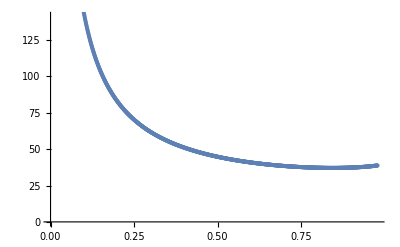

```mathematica
ListPlot[r4data]
```

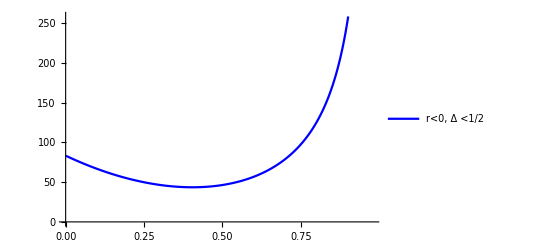

```mathematica
A0p = ListLinePlot[{#[[1]],action[#[[2]],#[[1]]]}& /@ r0data,
PlotStyle->{Blue}, PlotLegends->{"r<0, Δ <1/2"}]
```

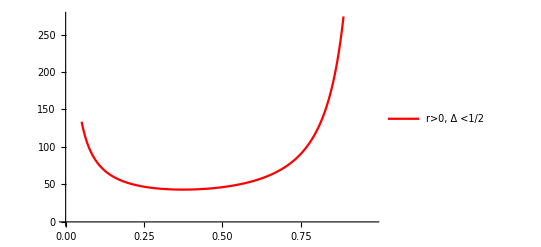

```mathematica
A2p = ListLinePlot[{#[[1]],action[#[[2]],#[[1]]]}& /@ r4data,
PlotStyle->{Red}, PlotLegends->{"r>0, Δ <1/2"}
]
```

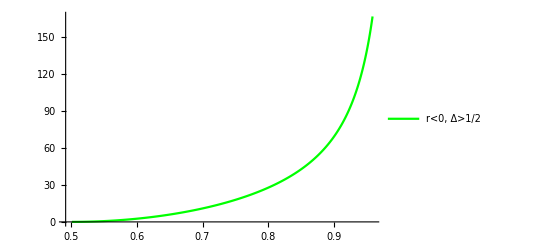

```mathematica
A1p = ListLinePlot[{#[[1]],action[#[[2]],#[[1]]]}& /@ r1data,
PlotStyle->{Green}, PlotLegends->{"r<0, Δ>1/2"}
]
```

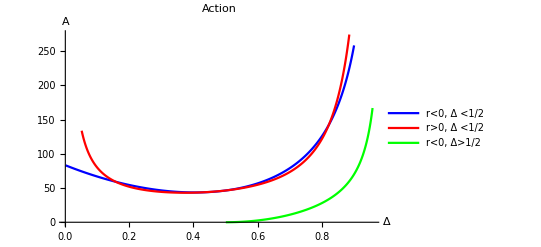

```mathematica
Show[{A0p,A2p, A1p},PlotRange->All,
PlotLabel->"Action", AxesLabel->{Δ, A}]
```

```mathematica
f1data = {#[[1]], #[[2]](1-#[[1]])}&/@ r1data;
```

```mathematica
AppendTo[f1data,{1,-6}];
```

```mathematica
f1data[[-10;;]]
```

{{0.951,-7.26394},{0.952,-7.28906},{0.953,-7.31447},{0.954,-7.34019},{0.955,-7.36622},{0.956,-7.39257},{0.957,-7.41925},{0.958,-7.44628},{0.959,-7.47368},{1,-6}}

```mathematica
interp0 = Interpolation[r0data];
interp1 = Interpolation[f1data];
interp2 = Interpolation[r4data];
```

```mathematica
d=.;
```

```mathematica
Δ1=Re[d/.FindRoot[action[interp2[d],d]- action[interp0[d],d],{d,0.156}][[1]]]
```

0.157143

```mathematica
Δ2=Re[d/.FindRoot[action[interp2[d],d]- action[interp0[d],d],{d,0.42}][[1]]]
```

0.43015

```mathematica
interp0[0.25]
```

-25.0706

```mathematica
Rfunc[d_]:= 
Piecewise[{
{interp0[d],0 <d <Δ1},
{interp2[d],Δ1 <=d <Δ2},
{interp0[d],Δ2 <=d <1/2},
{interp1[d]/(1-d),1/2 <=d <1}
}]//Quiet;
```

```mathematica
Rfunc[0.8]
```

-24.0743

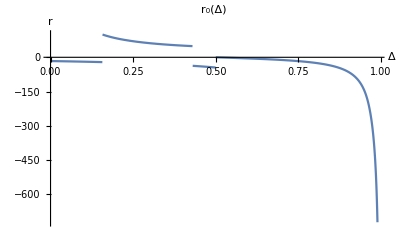

```mathematica
Plot[Rfunc[d],
{d,0,0.99},
PlotLabel->Subscript[r,0][Δ],
AxesLabel->{Δ,r},
PlotRange->All
]
```

InterpolatingFunction::dmval: Input value {0.0000202243} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

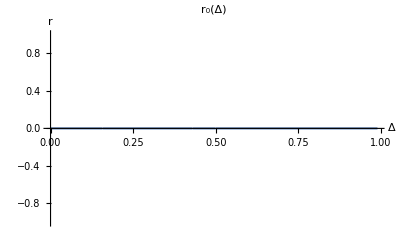

```mathematica
Plot[Im[gg[Rfunc[d],d]],
{d,0,0.99},
PlotLabel->Subscript[r,0][Δ],
AxesLabel->{Δ,r},
PlotRange->All
]
```

InterpolatingFunction::dmval: Input value {0.0000202243} lies outside the range of data in the interpolating function. Extrapolation will be used.

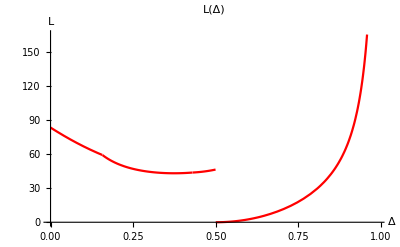

```mathematica
Plot[action[Rfunc[d],d],
{d,0,0.99},
PlotLabel->L[Δ],
AxesLabel->{Δ,L},
PlotStyle->{Red},
PlotRange->Automatic
]
```

```mathematica
Constraint[d_,  r_]:=
Block[{K1, K2, F1, F2,DF1, DF2, B, sol, x},
K1 =Sqrt[r/d ];
K2 =Sqrt[r/(d-1)];
(* x = ξ- ξ_2*);
F1 = Cos[K1 x] + B Sin[K1 x]/K1;
F2 = Cos[K2 x] + B Sin[K2 x]/K2;
DF1= D[F1,x];
DF2 = D[F2,x];
sol =Solve[{ (DF1/.x->-d)== (DF2/.x->1-d)}, B][[1]];
test = FullSimplify[Integrate[(F1/.sol),{x,-d,0}]/d+Integrate[(F2/.sol),{x, 0,1-d}]/(d-1)];
Print["linear term = ", test];
FullSimplify[Integrate[(F1/.sol)^2/2,{x,-d,0}]/d+Integrate[(F2/.sol)^2/2,{x, 0,1-d}]/(d-1)]
]
```

```mathematica
cons[Δ_, r_] =Constraint[Δ,r];
```

linear term = 0

```mathematica
cons[Δ,Rfunc[Δ]]/.Δ->0.3
```

0.359144+0. ⅈ

InterpolatingFunction::dmval: Input value {0.00002002} lies outside the range of data in the interpolating function. Extrapolation will be used.

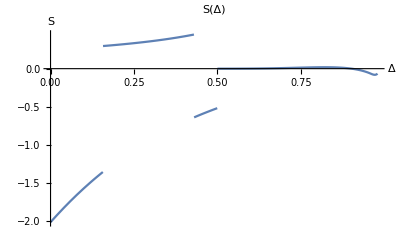

```mathematica
Plot[Re[cons[Δ, Rfunc[Δ]]],{Δ,0, 0.98}, 
PlotLabel->S[Δ],
AxesLabel->{Δ,S},
PlotRange->All
]
```

```mathematica
""
```

```mathematica
AlphaAlpha[d_,  r_]:=
Block[{K1, K2, F1, F2,DF1, DF2, B, sol, x},
K1 =Sqrt[r/d ];
K2 =Sqrt[r/(d-1)];
(* x = ξ- ξ_2*);
F1 = Cos[K1 x] + B Sin[K1 x]/K1;
F2 = Cos[K2 x] + B Sin[K2 x]/K2;
DF1= D[F1,x];
DF2 = D[F2,x];
sol =Solve[{ (DF1/.x->-d)== (DF2/.x->1-d)}, B][[1]];
FullSimplify[((DF1/.x->-d)(DF2/.x->0))/.sol,{r >0, 0 < d < 1 }]
]
```

```mathematica
αα[Δ_,r_]= AlphaAlpha[Δ,r]
```

(r (Δ Sin[√(r (-1+Δ))]-√((-1+Δ) Δ) Sin[√(r Δ)]) (Δ Cos[√(r Δ)] Sin[√(r (-1+Δ))]-√((-1+Δ) Δ) Cos[√(r (-1+Δ))] Sin[√(r Δ)]))/((-1+Δ) Δ^2 (Cos[√(r (-1+Δ))]-Cos[√(r Δ)])^2)

InterpolatingFunction::dmval: Input value {0.0000202243} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

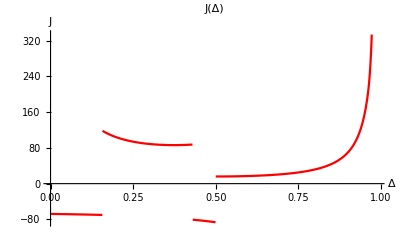

```mathematica
Plot[Re[αα[Δ, Rfunc[Δ]]],{Δ,0, 0.99},
PlotStyle->{Red}, 
PlotLabel->J[Δ],
AxesLabel->{Δ,J},
PlotRange->Automatic
]
```

```mathematica
SpectrumEq1[d_,  ω_, r_]:=
Block[{K, F1, F2,DF1, DF2,IF1, IF2, B1, B2, F,a, sol, x},
K =Sqrt[ ω];
(* x = ξ- ξ_2*);
F1 = r /( d ω) +B1 Cos[K x] + a Sin[K x];
F2 = r /( (d-1)ω) +B2 Cos[K x] + a Sin[K x];
DF1 = D[F1,x];
DF2 = D[F2,x];
IF1 = Integrate[F1,{x,-d,0}] /d;
IF2 = Integrate[F2,{x,0,1-d}] /(d-1);
(*Print[DF1];
Print[DF2];
Print[IF1];
Print[IF2];*)
Eq =
{1 == IF1+  IF2,
 (F1/.x->0)== (F2/.x->0),
 (F1/.x->-d)== (F2/.x->1-d)
};
sol =Solve[Eq,{B1, B2, a}][[1]];
Print[FullSimplify[{B1, B2, a}/.sol]];
FullSimplify[ ((DF1/.x->-d)- (DF2/.x->1-d))/.sol]
]
```

```mathematica
Eq1 =Numerator[SpectrumEq1[Δ,  ω, r]/(2 r)]//FullSimplify
```

{(Csc[(√ω)/2]^2 (-r (1+Δ) (-1+Cos[(-1+Δ) √ω])+2 r (-1+Δ) Cos[Δ √ω] Sin[1/2 (-1+Δ) √ω]^2-(-1+Δ) Δ √ω (r+(-1+Δ) Δ ω) Sin[(-1+Δ) √ω]+Δ ((-1+Δ) √ω (r+(-1+Δ) Δ ω)-r Sin[(-1+Δ) √ω]) Sin[Δ √ω]))/(2 (-1+Δ) Δ ω (-1+2 Δ+Csc[(√ω)/2] Sin[1/2 (1-2 Δ) √ω])),(Csc[(√ω)/2]^2 (-r (-2+Δ)+r Δ Cos[(-1+Δ) √ω] (-1+Cos[Δ √ω])+r (-2+Δ) Cos[Δ √ω]+(-1+Δ) (Δ √ω (r+(-1+Δ) Δ ω) Sin[Δ √ω]+Sin[(-1+Δ) √ω] (-Δ √ω (r+(-1+Δ) Δ ω)+r Sin[Δ √ω]))))/(2 (-1+Δ) Δ ω (-1+2 Δ+Csc[(√ω)/2] Sin[1/2 (1-2 Δ) √ω])),-((Csc[(√ω)/2] (-r Δ Sin[(-1+Δ) √ω]+Cos[Δ √ω] (-((-1+Δ) Δ √ω (r+(-1+Δ) Δ ω))+r Δ Sin[(-1+Δ) √ω])+r (-1+Δ) Sin[Δ √ω]+(-1+Δ) Cos[(-1+Δ) √ω] (Δ √ω (r+(-1+Δ) Δ ω)-r Sin[Δ √ω])))/(2 (-1+Δ) Δ ω ((-1+2 Δ) Sin[(√ω)/2]+Sin[1/2 (1-2 Δ) √ω])))}

-r Cos[(√ω)/2]+r Cos[1/2 (1-2 Δ) √ω]+(-1+Δ) Δ √ω (r+(-1+Δ) Δ ω) Sin[(√ω)/2]

```mathematica
f[ω_,  r_, Δ_] = Eq1
```

-r Cos[(√ω)/2]+r Cos[1/2 (1-2 Δ) √ω]+(-1+Δ) Δ √ω (r+(-1+Δ) Δ ω) Sin[(√ω)/2]

```mathematica
-r Cos[(√ω)/2]+r Cos[1/2 (1-2 Δ) √ω]+(-1+Δ) Δ √ω (r+(-1+Δ) Δ ω) Sin[(√ω)/2]
```

-r Cos[(√ω)/2]+r Cos[1/2 (1-2 Δ) √ω]+(-1+Δ) Δ √ω (r+(-1+Δ) Δ ω) Sin[(√ω)/2]

```mathematica
PhiPlot[d_, L_]:=
Block[{ w,x, Phi},
Phi[ w_]= f[w,Rfunc[d],d]/Cos[Sqrt[w]/2](w)^(-3/2 );
Plot[Arg[Phi[I x]]/Pi,{x,-L,L},
PlotLabel->Arg[Φ[I x]] ,
PlotStyle->{Red,Green},
PlotLegends->{Re,Im}]
]
```

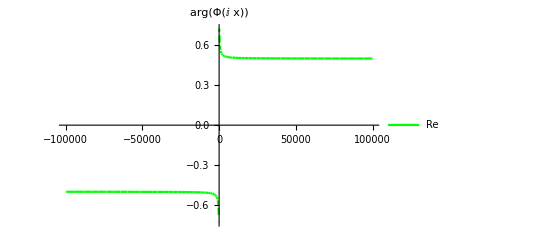

```mathematica
PhiPlot[0.4,100000]
```

```mathematica
RePlot[d_, L_]:=
Block[{ w,x, Phi, r},
r = Rfunc[d];
Phi[ w_]= f[w,r,d]/Cos[Sqrt[w]/2](w)^(-3/2 );
Plot[Re[Phi[I x]]x/(d(d-1)r),{x,-L,L},
PlotLabel->Re[Φ[I x]]  ,
PlotStyle->{Green},
PlotLegends->{Re}]
]
```

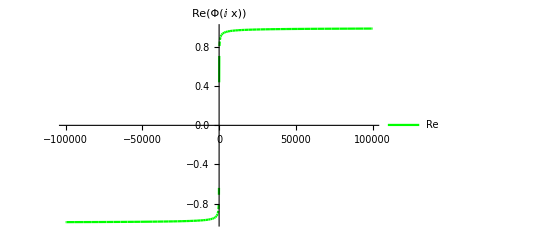

```mathematica
RP =RePlot[0.4,100000]
```

```mathematica
ImPlot[d_, L_]:=
Block[{ w,x, Phi},
Phi[ w_]= f[w,Rfunc[d],d]/Cos[Sqrt[w]/2](w)^(-3/2 );
Plot[Im[Phi[I x]]/(d(1-d))^2,{x,-L,L},
PlotLabel->Im[Φ[I x]] ,
PlotStyle->{Red},
PlotLegends->{Im}]
]
```

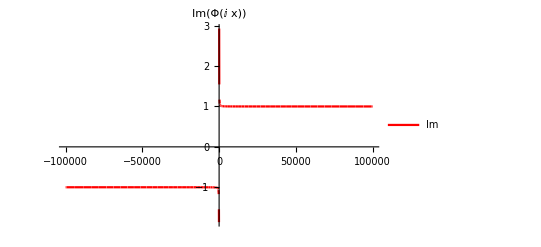

```mathematica
IP =ImPlot[0.4,100000]
```

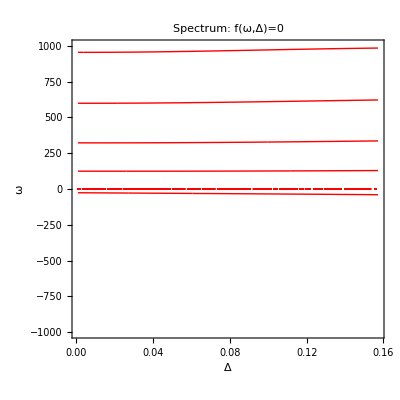

```mathematica
CP0=ContourPlot[Re[f[ω,interp0[Δ],Δ]]==0,{Δ, 0.001,Δ1},{ω,-1000,1000},
MaxRecursion->5,
PlotPoints->100,
AxesLabel->{Δ, ω},
GridLines->{Range[100]/100,Automatic},
GridLinesStyle->Directive[Gray,Dashed],
PlotLabel->"Spectrum: f(ω,Δ)=0",
ContourStyle->{Red, Thick}]
```

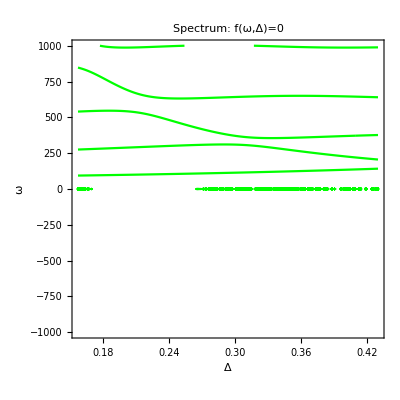

```mathematica
CP1=ContourPlot[Re[f[ω, interp2[Δ],Δ ]]==0,{Δ, Δ1,Δ2},{ω,-1000,1000},
MaxRecursion->5,
PlotPoints->100,
AxesLabel->{Δ, ω},
GridLines->{Range[100]/100,Automatic},
GridLinesStyle->Directive[Gray,Dashed],
PlotLabel->"Spectrum: f(ω,Δ)=0",
ContourStyle->{Green}]
```

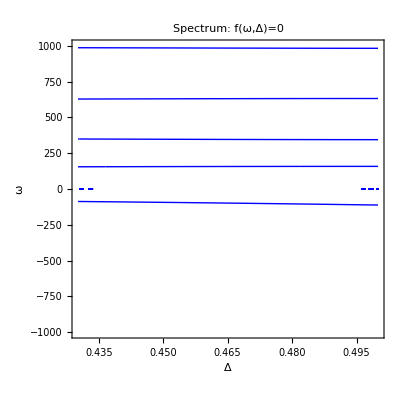

```mathematica
CP2=ContourPlot[Re[f[ω , interp0[Δ],Δ]]==0,{Δ, Δ2,1/2},{ω,-1000,1000},
MaxRecursion->5,
PlotPoints->100,
AxesLabel->{Δ, ω},
GridLines->{Range[100]/100,Automatic},
GridLinesStyle->Directive[Gray,Dashed],
PlotLabel->"Spectrum: f(ω,Δ)=0",
ContourStyle->{Blue, Thick}]
```

InterpolatingFunction::dmval: Input value {0.500005} lies outside the range of data in the interpolating function. Extrapolation will be used.

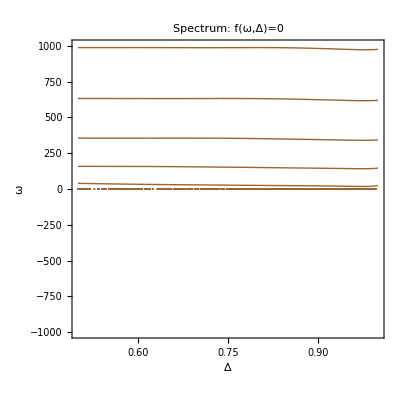

```mathematica
CP3=ContourPlot[Re[f[ω , interp1[Δ],Δ]]==0,{Δ, 1/2,1},{ω,-1000,1000},
MaxRecursion->5,
PlotPoints->100,
AxesLabel->{Δ, ω},
GridLines->{Range[100]/100,Automatic},
GridLinesStyle->Directive[Gray,Dashed],
PlotLabel->"Spectrum: f(ω,Δ)=0",
ContourStyle->{Brown, Thick}]
```

```mathematica
Show[{CP0,CP1,CP2,CP3},AxesLabel->{Δ, ω},PlotRange->Automatic]
```

-Graphics-

```mathematica
cond =0 <x1 < x3 < x2 < 1 ;
F = .;
```

```mathematica
G1[x_] :=1/2Abs[x-x3] + A + B (x -x2)+ r F (x-x2)^2/(2(x2-x1)); 
G2[x_] := 1/2Abs[x-x3] +A + B (x -x2)+  r F (x-x2)^2/(2(x2-x1-1)); 
GP1[x_] :=1/2Sign[x-x3] + B + r F (x-x2)/(x2-x1); 
GP2[x_] := 1/2Sign[x-x3]+ B +  r F (x-x2)/(x2-x1-1);
```

```mathematica
(*Assuming[cond,Integrate[G1[x],{x,x1,x2}]] + Integrate[G2[x],{x,x2,1+x1}]*)
Eqs = 
FullSimplify[{-F + Assuming[cond,Integrate[G1[x],{x,x1,x2},GenerateConditions->False]/(x2-x1) + Integrate[G2[x],{x,x2,1+x1},GenerateConditions->False]/(x2-x1-1)], 
 G2[1 + x1],
(G1[x1])/.{Sign[x1-x3]->-1,Abs[x1-x3]-> x3 - x1}
}/.{Abs[x2-x3]->x2-x3,Abs[x1-x3]->x3-x1, Abs[1+x1-x3]->1+ x1-x3, Sign[1+x1-x3]->1}]
```

{(-6 x1^2+(3+6 B-2 F (-6+r)) x2-6 x3^2+x1 (-3-6 B+2 F (-6+r)+12 x3))/(12 (x1-x2)),1/2 (1+2 A+x1+2 B (1+x1-x2)+F r (-1-x1+x2)-x3),1/2 (2 A+(-1+2 B-F r) x1-2 B x2+F r x2+x3)}

```mathematica
Eqs
```

{(-6 x1^2+(3+6 B-2 F (-6+r)) x2-6 x3^2+x1 (-3-6 B+2 F (-6+r)+12 x3))/(12 (x1-x2)),1/2 (1+2 A+x1+2 B (1+x1-x2)+F r (-1-x1+x2)-x3),1/2 (2 A+(-1+2 B-F r) x1-2 B x2+F r x2+x3)}

```mathematica
sol =FullSimplify[Solve[{Eqs[[1]]==0,Eqs[[2]]==0, Eqs[[3]]==0},{A,B,F}],cond][[1]]
```

{A→x1^2+x2 (-1/2+x3)-x3/2-x1 (-1+x2+x3),B→1/(2 (12+r) (x1-x2))(-2 (12+r) x1^2-x1 (12+r+4 (-6+r) x2)+8 (3+r) x1 x3-6 r x3^2+x2 (12+r+4 (-6+r) x3)),F→(6 (x1-x3) (-x2+x3))/((12+r) (x1-x2))}

```mathematica
FullSimplify[D[GP1[x1]/.sol,x3]/.{Sign'[x1-x3]->0,  x3-> x2},cond]
```

-2+36/(12+r)

```mathematica
Factor[-2+36/(12+r)]
```

-(2 (-6+r))/(12+r)

```mathematica
g =FullSimplify[G1[x]/.sol]
```

1/2 (2 x1^2+(6 r (x-x2)^2 (x1-x3) (x2-x3))/((12+r) (x1-x2)^2)-x3-2 x1 (-1+x2+x3)+x2 (-1+2 x3)+1/((12+r) (x1-x2))(x-x2) (-2 (12+r) x1^2-x1 (12+r+4 (-6+r) x2)+8 (3+r) x1 x3-6 r x3^2+x2 (12+r+4 (-6+r) x3))+Abs[x-x3])

```mathematica
FullSimplify[(g/.x->x1)/.Abs[x1-x3] -> x3-x1]
```

0

```mathematica
FullSimplify[(g/.{x3->x2})/.{Abs[x2-x3] -> x2-x3,Abs[x-x2]->x2-x}]
```

-((x-x1) (1+x1-x2))

```mathematica
KKK =(Q Sqrt[r]/τ^3 Integrate[x^2(x J/S  - 2 (6-r)/(12+r))Exp[- x L/(2 Pi S)],{x,κ τ,Infinity},GenerateConditions->False] )//FullSimplify
```

1/(L^4 (12+r) τ^3)2 ⅇ^(-(L κ τ)/(2 π S)) π Q √r (16 π^2 (L (-6+r)+3 J π (12+r)) S^3+8 L π (L (-6+r)+3 J π (12+r)) S^2 κ τ+2 L^2 (L (-6+r)+3 J π (12+r)) S κ^2 τ^2+J L^3 (12+r) κ^3 τ^3)

```mathematica
FullSimplify[1/(L^4 (12+r) τ^3)2 ⅇ^(-(L κ τ)/(2 π S)) π Q √r]
```

(2 ⅇ^(-(L κ τ)/(2 π S)) π Q √r)/(L^4 (12+r) τ^3)

```mathematica
FullSimplify /@CoefficientList[16 π^2 (L (-6+r)+3 J π (12+r)) S^3+8 L π (L (-6+r)+3 J π (12+r)) S^2 κ τ+2 L^2 (L (-6+r)+3 J π (12+r)) S κ^2 τ^2+J L^3 (12+r) κ^3 τ^3,τ]
```

{16 π^2 (L (-6+r)+3 J π (12+r)) S^3,8 L π (L (-6+r)+3 J π (12+r)) S^2 κ,2 L^2 (L (-6+r)+3 J π (12+r)) S κ^2,J L^3 (12+r) κ^3}

```mathematica
KKK0 =FullSimplify[ KKK/.{κ->0}]
```

(32 π^3 Q √r (L (-6+r)+3 J π (12+r)) S^3)/(L^4 (12+r) τ^3)

```mathematica
IKKK0 =Integrate[(τ^5/n^5 - τ^(10))τ^(1/2-2)KKK0,{τ,0,1/n},GenerateConditions->False]//FullSimplify
```

(640 (1/n)^(13/2) π^3 Q √r (L (-6+r)+3 J π (12+r)) S^3)/(39 L^4 (12+r))

```mathematica
SumKK0[Q_, S_, L_, J_,r_]= (IKKK0/.n->1)Sum[ EulerPhi[n]n^(-13/2),{n,1,Infinity}]
```

(640 π^3 Q √r (L (-6+r)+3 J π (12+r)) S^3 Zeta[11/2])/(39 L^4 (12+r) Zeta[13/2])

```mathematica
W[n_, κ_, Q_, S_, L_, J_,r_] =FullSimplify[Integrate[(τ^5/n^5 - τ^(10))τ^(1/2-2)(KKK-KKK0),{τ,0,1/n},GenerateConditions->False]]
```

-1/(39 L^(21/2) (12+r) κ^(13/2))2 (1/n)^(11/2) π^3 Q √r S^2 (-10 ⅇ^(-(L κ)/(2 n π S)) √L √κ (392837445 J n^5 π^7 (12+r) S^7+6891885 L n^4 π^6 S^6 (6 n (-6+r) S+19 J (12+r) κ)+1378377 L^2 n^3 π^5 S^5 κ (10 n (-6+r) S+19 J (12+r) κ)+196911 L^3 n^2 π^4 S^4 κ^2 (14 n (-6+r) S+19 J (12+r) κ)+21879 L^4 n π^3 S^3 κ^3 (18 n (-6+r) S+19 J (12+r) κ)+(2 L^7 κ^6 (-2 (-39+8 ⅇ^((L κ)/(2 n π S))) n (-6+r) S+39 J (12+r) κ))/n^2+234 L^5 π^2 S^2 κ^4 (187 n (-6+r) S+151 J (12+r) κ)+(24 L^6 π S κ^5 (143 n (-6+r) S-(-91+4 ⅇ^((L κ)/(2 n π S))) J (12+r) κ))/n)+1365 √2 √n π^2 S^(5/2) (75735 n^5 π^5 (2 L (-6+r)+19 J π (12+r)) S^5-L^5 (2 L (-6+r)+9 J π (12+r)) κ^5) Erf[(√L √κ)/(√n √(2 π) √S)])

```mathematica
test =Limit[ W[n, κ, Q, S, L, J,r],κ->0]
```

0

```mathematica
W1[n_, κ_, Q_, S_, L_, J_,r_] := IKKK0 + FullSimplify /@Collect[Normal[Series[W[n, κ, Q, S, L, J,r],{κ,0,12}]],κ]
```

```mathematica
W1[n, κ, Q, S, L, J,r]
```

```mathematica
(640 (1/n)^(13/2) π^3 Q √r (L (-6+r)+3 J π (12+r)) S^3)/(39 L^4 (12+r))-(40 (1/n)^(19/2) Q (-6+r) √r κ^3)/(513 (12+r))-(5 (1/n)^(21/2) Q √r (-L (-6+r)+J π (12+r)) κ^4)/(231 π (12+r) S)+(L (1/n)^(23/2) Q √r (-L (-6+r)+2 J π (12+r)) κ^5)/(299 π^2 (12+r) S^2)+(L^2 (1/n)^(25/2) Q √r (L (-6+r)-3 J π (12+r)) κ^6)/(2700 π^3 (12+r) S^3)+(5 L^3 (1/n)^(27/2) Q √r (-L (-6+r)+4 J π (12+r)) κ^7)/(154224 π^4 (12+r) S^4)+(L^4 (1/n)^(29/2) Q √r (L (-6+r)-5 J π (12+r)) κ^8)/(423168 π^5 (12+r) S^5)
```

(640 (1/n)^(13/2) π^3 Q √r (L (-6+r)+3 J π (12+r)) S^3)/(39 L^4 (12+r))-(40 (1/n)^(19/2) Q (-6+r) √r κ^3)/(513 (12+r))-(5 (1/n)^(21/2) Q √r (-L (-6+r)+J π (12+r)) κ^4)/(231 π (12+r) S)+(L (1/n)^(23/2) Q √r (-L (-6+r)+2 J π (12+r)) κ^5)/(299 π^2 (12+r) S^2)+(L^2 (1/n)^(25/2) Q √r (L (-6+r)-3 J π (12+r)) κ^6)/(2700 π^3 (12+r) S^3)+(5 L^3 (1/n)^(27/2) Q √r (-L (-6+r)+4 J π (12+r)) κ^7)/(154224 π^4 (12+r) S^4)+(L^4 (1/n)^(29/2) Q √r (L (-6+r)-5 J π (12+r)) κ^8)/(423168 π^5 (12+r) S^5)

```mathematica
SS[a_] := Evaluate[Sum[EulerPhi[n]/n^a,{n,1,Infinity}]]
```

```mathematica
SS[a]
```

Zeta[-1+a]/Zeta[a]

```mathematica
IH5 =W1[n, κ, Q, S, L, J,r]/.(1/n)^a_ :> SS[a]
```

(640 π^3 Q √r (L (-6+r)+3 J π (12+r)) S^3 Zeta[11/2])/(39 L^4 (12+r) Zeta[13/2])-(40 Q (-6+r) √r κ^3 Zeta[17/2])/(513 (12+r) Zeta[19/2])-(5 Q √r (-L (-6+r)+J π (12+r)) κ^4 Zeta[19/2])/(231 π (12+r) S Zeta[21/2])+(L Q √r (-L (-6+r)+2 J π (12+r)) κ^5 Zeta[21/2])/(299 π^2 (12+r) S^2 Zeta[23/2])+(L^2 Q √r (L (-6+r)-3 J π (12+r)) κ^6 Zeta[23/2])/(2700 π^3 (12+r) S^3 Zeta[25/2])+(5 L^3 Q √r (-L (-6+r)+4 J π (12+r)) κ^7 Zeta[25/2])/(154224 π^4 (12+r) S^4 Zeta[27/2])+(L^4 Q √r (L (-6+r)-5 J π (12+r)) κ^8 Zeta[27/2])/(423168 π^5 (12+r) S^5 Zeta[29/2])+(L^5 Q √r (-L (-6+r)+6 J π (12+r)) κ^9 Zeta[29/2])/(6749568 π^6 (12+r) S^6 Zeta[31/2])+(L^6 Q √r (L (-6+r)-7 J π (12+r)) κ^10 Zeta[31/2])/(122411520 π^7 (12+r) S^7 Zeta[33/2])+(L^7 Q √r (-L (-6+r)+8 J π (12+r)) κ^11 Zeta[33/2])/(2483712000 π^8 (12+r) S^8 Zeta[35/2])+(L^8 Q √r (L (-6+r)-9 J π (12+r)) κ^12 Zeta[35/2])/(55682629632 π^9 (12+r) S^9 Zeta[37/2])

```mathematica
IHCoef = .;
```

```mathematica
IHCoef= CoefficientList[IH5,κ]
```

{(640 π^3 Q √r (L (-6+r)+3 J π (12+r)) S^3 Zeta[11/2])/(39 L^4 (12+r) Zeta[13/2]),0,0,-(40 Q (-6+r) √r Zeta[17/2])/(513 (12+r) Zeta[19/2]),-(5 Q √r (-L (-6+r)+J π (12+r)) Zeta[19/2])/(231 π (12+r) S Zeta[21/2]),(L Q √r (-L (-6+r)+2 J π (12+r)) Zeta[21/2])/(299 π^2 (12+r) S^2 Zeta[23/2]),(L^2 Q √r (L (-6+r)-3 J π (12+r)) Zeta[23/2])/(2700 π^3 (12+r) S^3 Zeta[25/2]),(5 L^3 Q √r (-L (-6+r)+4 J π (12+r)) Zeta[25/2])/(154224 π^4 (12+r) S^4 Zeta[27/2]),(L^4 Q √r (L (-6+r)-5 J π (12+r)) Zeta[27/2])/(423168 π^5 (12+r) S^5 Zeta[29/2]),(L^5 Q √r (-L (-6+r)+6 J π (12+r)) Zeta[29/2])/(6749568 π^6 (12+r) S^6 Zeta[31/2]),(L^6 Q √r (L (-6+r)-7 J π (12+r)) Zeta[31/2])/(122411520 π^7 (12+r) S^7 Zeta[33/2]),(L^7 Q √r (-L (-6+r)+8 J π (12+r)) Zeta[33/2])/(2483712000 π^8 (12+r) S^8 Zeta[35/2]),(L^8 Q √r (L (-6+r)-9 J π (12+r)) Zeta[35/2])/(55682629632 π^9 (12+r) S^9 Zeta[37/2])}

```mathematica
IQ[ Δ_] :=
Module[{r,L,S,J, Q, ω, Phi, FF, eps = 0.1},
r = interp2[Δ];
(*Print[r];*)
Phi =D[Log[ f[ω,r,Δ]/(Cos[Sqrt[ω]/2] ω^(3/2))],ω];
(*Print[{Phi/.{ω->eps-I L},Phi/.{ω->eps+I L}}];*)
NIntegrate[ Re[(Phi Log[ω])/.ω->eps+I x],{x,-Infinity, Infinity},
Method->"DoubleExponentialOscillatory"]
]//Quiet;
```

```mathematica
qtab = ParallelTable[{Δ,IQ[ Δ]},{Δ,Δ1,Δ2,0.00005}];
```

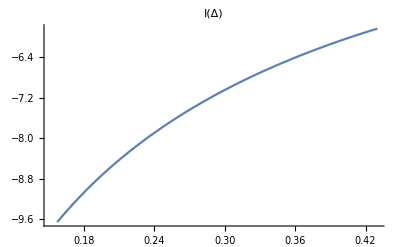

```mathematica
ListLinePlot[qtab, PlotLabel->"I(Δ)"]
```

```mathematica
iqinterp = Interpolation[qtab];
```

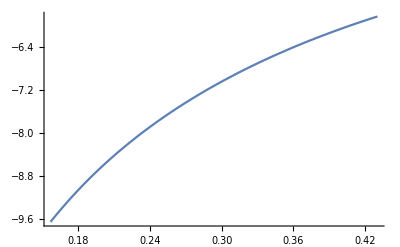

```mathematica
Plot[iqinterp[x],{x,Δ1,Δ2}]
```

```mathematica
interp2
```

InterpolatingFunction[…]

```mathematica
interp2[0.25]
```

70.2248

```mathematica
r =.;
```

```mathematica
H9[Δ_] :=Module[{Sub},
Sub = 
{r -> interp2[Δ],
L ->Re[action[r,Δ]],
S-> Re[αα[Δ, r]],
J -> Re[cons[Δ, r]],
Q -> Exp[1/(8 Pi)iqinterp[Δ]]
};
CoefficientList[(1-Δ)IH5//.Sub, κ]
];
```

```mathematica
H9[0.25]
```

{16159.7,0,0,-0.28179,0.0120844,-0.000288313,4.92626×10^-6,-6.64749×10^-8,7.46191×10^-10,-7.19671×10^-12,6.09706×10^-14,-4.61125×10^-16,3.15195×10^-18}

```mathematica
h9tab = Block[{delta=0.0001, tab, interp},
tab = ParallelTable[{Δ,H9[Δ]},{Δ,Δ1,Δ2,delta}];
interp = Interpolation[tab,InterpolationOrder->5];
Integrate[interp[Δ],{Δ,Δ1,Δ2}]
]
```

InterpolatingFunction::dmvali: The integration endpoint 0.43015 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

{4057.07,0.,0.,-0.0702749,0.00300616,-0.0000715309,1.21875×10^-6,-1.6396×10^-8,1.83452×10^-10,-1.76318×10^-12,1.48819×10^-14,-1.12099×10^-16,7.629×10^-19}

```mathematica
Z
```

7.56011×10^6

```mathematica
h9[κ_] := Sum[h9tab[[l]]/Z κ^(l-1),{l,1,Length[h9tab]}]
```

```mathematica
h9[κ]
```

0.000536642-9.29549×10^-9 κ^3+3.97634×10^-10 κ^4-9.46163×10^-12 κ^5+1.61208×10^-13 κ^6-2.16876×10^-15 κ^7+2.42658×10^-17 κ^8-2.33221×10^-19 κ^9+1.96847×10^-21 κ^10-1.48277×10^-23 κ^11+1.00911×10^-25 κ^12

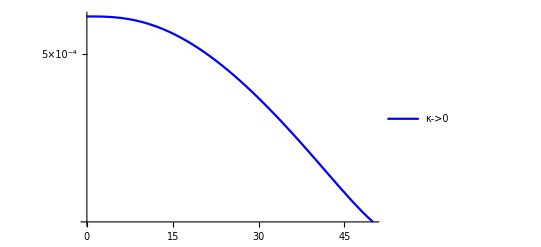

```mathematica
h9Plot =LogPlot[h9[κ],{κ,0,50},PlotStyle->{Blue},
PlotLegends->{"κ->0"}]
```

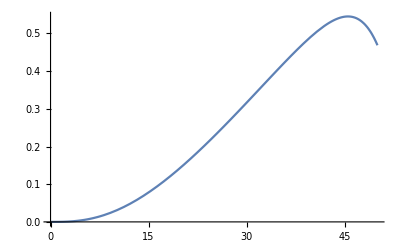

```mathematica
Plot[-κ h9'[κ]/h9[κ],{κ,0,50}]
```

```mathematica
H[κ_, Δ_] :=
Module[{r,L,S,J, Q, ω, Phi, FF, eps = 0.1},
r = interp2[Δ];
(*Print[r];*)
L = Re[action[r,Δ]];
(*Print[L];*)
S= Re[αα[Δ, r]];
(*Print[S];*)
J = Re[cons[Δ, r]];
(*Print[J];*)
Q = Exp[1/(8 Pi)iqinterp[Δ]];
If[κ==0,(1-Δ)SumKK0[Q, S, L, J,r],
(1-Δ)(SumKK0[Q, S, L, J,r] + NSum[EulerPhi[n] W[n, κ, Q, S, L, J,r],{n,1,Infinity}])
]
]//Quiet;
```

```mathematica
H[0, 0.4]//Timing
```

{0.001067,11203.6}

```mathematica
H[50, 0.4]
```

7537.59

```mathematica
H[10, 0.2]//Timing
```

{30.4057,18250.1}

```mathematica
Z =  Block[{delta=0.0001, tab, interp},
tab = ParallelTable[H[0, Δ],{Δ,Δ1,Δ2,delta}];
interp = Interpolation[tab,InterpolationOrder->5];
4*Pi *864 Zeta[3]/Pi^2Integrate[interp[Δ],{Δ,Δ1,Δ2}]
]
```

InterpolatingFunction::dmvali: The integration endpoint 0.157143 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmvali: The integration endpoint 0.43015 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

7.56011×10^6

```mathematica
Z
```

7.56011×10^6

```mathematica
{Δ1, Δ2}
```

{0.157143,0.43015}

```mathematica
{0.15714261196307505,0.4301495990065511}
```

{0.157143,0.43015}

```mathematica
II =FullSimplify[Integrate[t^(5/2)(2(r-6)/(r+12) + J/S t x) E^(- L t x/(2 Pi S)),{t,0,Infinity},GenerateConditions->False], {x >0,L >0, S >0}]
```

(15 √2 π^4 (2 L (-6+r)+7 J π (12+r)) (S/x)^(7/2))/(L^(9/2) (12+r))

```mathematica
JJ = II Sum[EulerPhi[n]/n^5,{n,1,Infinity}]
```

(π^8 (2 L (-6+r)+7 J π (12+r)) (S/x)^(7/2))/(3 √2 L^(9/2) (12+r) Zeta[5])

```mathematica
test=Integrate[x^2JJ/Z,{x, κ, Infinity}, GenerateConditions->False]
```

(0.00057058 (2 L (-6+r)+7 J π (12+r)) S^(7/2) √(1/κ))/(L^(9/2) (12+r))

```mathematica
H0[κ_]:= test;
```

```mathematica
KK = FullSimplify[3/Pi^2Integrate[-t^(15/2-2)(2(r-6)/(r+12) + J/S t x) E^(- L t x/(2 Pi S)),{t,0,Infinity},GenerateConditions->False], {x >0,L >0, S >0}]
```

-(31185 √2 π^6 ((2 L (-6+r) x)/π+13 J (12+r) x))/((12+r) S ((L x)/S)^(15/2))

```mathematica
KK1 =( KK/.x->1)/x^(13/2)
```

-(31185 √2 π^6 ((2 L (-6+r))/π+13 J (12+r)))/((12+r) (L/S)^(15/2) S x^(13/2))

```mathematica
Integrate[x^2KK/Z,{x, κ, Infinity}, GenerateConditions->False]
```

-(1.0201 (L (-6.+1. r)+J (245.044+20.4204 r)) √(L/S) S^7 (1/κ)^(7/2))/(L^8 (12.+r))

```mathematica
Hinf[Δ_] :=Module[{Sub},
Sub = 
{x->1, 
r -> interp2[Δ],
L ->Re[action[r,Δ]],
S-> Re[αα[Δ, r]],
J -> Re[cons[Δ, r]],
Q -> Exp[1/(8 Pi)iqinterp[Δ]]
};
((1-Δ)JJ/Z)//.Sub
];

Hinf[0.25]
```

0.00416069

```mathematica
hinf =Block[{delta=0.0001, tab, interp},
tab = ParallelTable[{Δ,Hinf[Δ]},{Δ,Δ1,Δ2,delta}];
interp = Interpolation[tab,InterpolationOrder->5];
Integrate[interp[Δ],{Δ,Δ1,Δ2}]
]
```

InterpolatingFunction::dmvali: The integration endpoint 0.43015 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

0.00106051

```mathematica
HinfCor[Δ_] := Module[{Sub},
Sub = 
{x->1, 
r -> interp2[Δ],
L ->Re[action[r,Δ]],
S-> Re[αα[Δ, r]],
J -> Re[cons[Δ, r]],
Q -> Exp[1/(8 Pi)iqinterp[Δ]]
};
((1-Δ)KK/Z)//.Sub
];
```

```mathematica
HinfCor[0.25]
```

-224.546

```mathematica
hinfCor =Block[{delta=0.0001, tab, interp},
tab = ParallelTable[{Δ,HinfCor[Δ]},{Δ,Δ1,Δ2,delta}];
interp = Interpolation[tab,InterpolationOrder->5];
Integrate[interp[Δ],{Δ,Δ1,Δ2}]
]
```

InterpolatingFunction::dmvali: The integration endpoint 0.43015 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

-57.6095

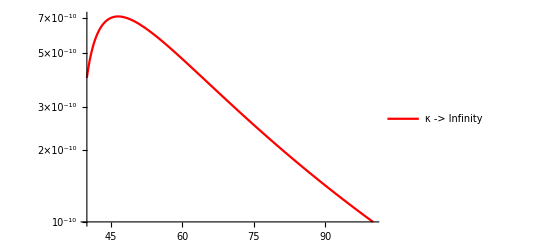

```mathematica
hinfPlot = LogPlot[hinf/κ^(7/2)+ hinfCor/κ^(13/2) ,{κ,40,100},
PlotStyle->{Red}, PlotLegends->{"κ -> Infinity"}]
```

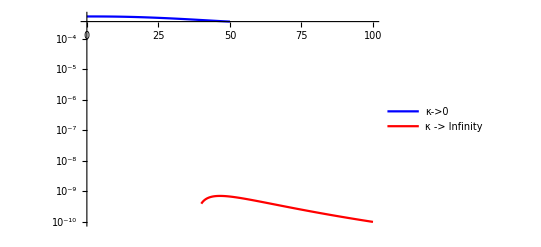

```mathematica
Show[{h9Plot,hinfPlot}, PlotRange->All]
```

```mathematica
hint[κ_] := hinf/κ^(7/2)+ hinfCor/κ^(13/2);
```

```mathematica
hint[κ]
```

-57.6095/κ^(13/2)+0.00106051/κ^(7/2)

```mathematica
F[κ_] =Integrate[hint[x] x^2,{x,κ,Infinity},GenerateConditions->False]
```

(-16.4599+0.00212102 κ^3)/κ^(7/2)

```mathematica
F[x]
```

(-16.4599+0.00212102 x^3)/x^(7/2)

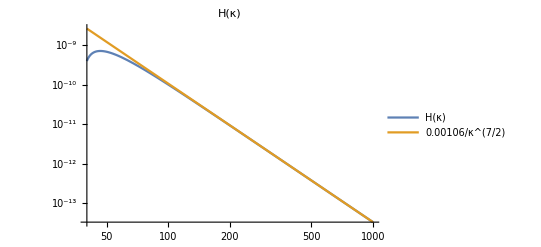

```mathematica
LogLogPlot[{hint[x],0.0010605107259500915/x^(7/2)},{x,40,1000}, 
PlotLabel->"H(κ)", PlotLegends->{"H(κ)",0.00106/κ^(7/2)}]
```

```mathematica
LE[T_] := Log[F[Sqrt[T]]] - 2 Log[T];
```

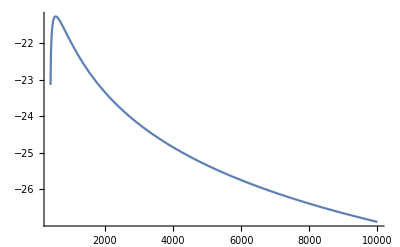

```mathematica
Plot[LE[T],{T,400,10000}]
```

```mathematica
ClearAll[n];
```

```mathematica
n[T_] := Evaluate[-T D[LE[T],T]-1];
```

```mathematica
n[150]
```

3.21523

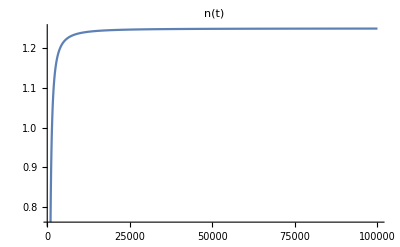

```mathematica
Plot[n[x], {x,1000,10^5},
PlotRange->All,PlotLabel->"n(t)"]
```

```mathematica
NPlot=Block[{T,t, t0=0, t1=1500, T0= 1 , T1= 15349, A, B},
T = T0 + (T1-T0)/(t1-t0)(t-t0);
A =Plot[n[T], {t,t0,6*t1},
PlotStyle->{Green},
PlotLegends->{"Dual Theory"},
PlotRange->{All, {1.,1.5}},PlotLabel->"n(t)"];
B = Plot[5/4,{t,t0,6*t1},
PlotStyle->{Red},
PlotRange->{All, {1.,1.5}},
PlotLegends->{5/4}];
Show[{B,A}]
];
```

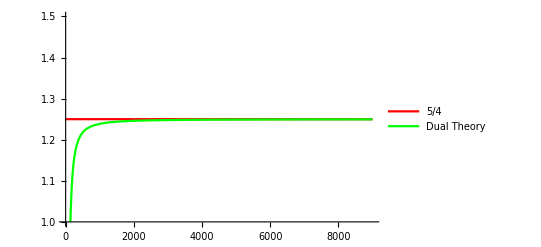

```mathematica
NPlot
```

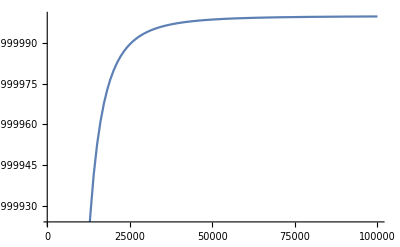

```mathematica
Plot[-k hint'[k]/hint[k],{k,1000,100000}]
```

```mathematica
SP[k_] :=hint[k];
```

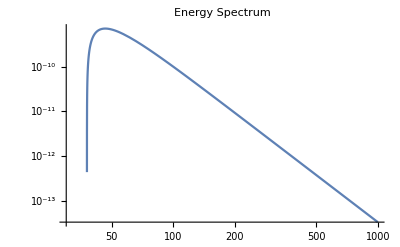

```mathematica
LogLogPlot[SP[k],{k,30,1000},PlotLabel->"Energy Spectrum"]
```

```mathematica
SPindex[k_] := -k hint'[k]/hint[k];
```

```mathematica
SIndexPlot=Block[{k, k0=30, k1=1000, A, B,D},
A = Plot[SPindex[k], {k,k0,k1},
PlotStyle->{Green},
PlotLegends->{"Dual Theory"},
PlotRange->{All, {1,5}},PlotLabel->"Spectrum Index(k)"];
B = Plot[7/2,{k,k0,k1},
PlotStyle->{Blue},
PlotRange->{All, {1,5}},
PlotLegends->{7/2}];
D = Plot[5/3,{k,k0,k1},
PlotStyle->{Red},
PlotRange->{All, {1,5}},
PlotLegends->{5/3}];
Show[{B,D,A},PlotLabel->"Energy Spectrum Index"]
];
```

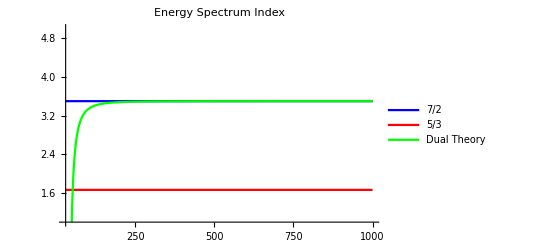

```mathematica
SIndexPlot
```

```mathematica
ff = TrigToExp[f[ω,r, Δ]/.Sqrt[ω] -> I Sqrt[-ω]];
```

```mathematica
Fas=FullSimplify /@TrigToExp[Expand[ff /Cosh[1/2 √-ω]/(-ω)^(3/2)]]
```

-Δ^2/(1+ⅇ^(√-ω))+(1-1/(1+ⅇ^(√-ω))) Δ^2+(2 Δ^3)/(1+ⅇ^(√-ω))+2 (-1+1/(1+ⅇ^(√-ω))) Δ^3-Δ^4/(1+ⅇ^(√-ω))+(1-1/(1+ⅇ^(√-ω))) Δ^4+(ⅇ^(-((-1+Δ) √-ω)) r)/((1+ⅇ^(√-ω)) (-ω)^(3/2))+(ⅇ^(Δ √-ω) r)/((1+ⅇ^(√-ω)) (-ω)^(3/2))+(r ω)/((1+ⅇ^(√-ω)) (-ω)^(5/2))+(ⅇ^(√-ω) r ω)/((1+ⅇ^(√-ω)) (-ω)^(5/2))+(r Δ)/(ω+ⅇ^(√-ω) ω)-(ⅇ^(√-ω) r Δ)/(ω+ⅇ^(√-ω) ω)-(r Δ^2)/(ω+ⅇ^(√-ω) ω)+(ⅇ^(√-ω) r Δ^2)/(ω+ⅇ^(√-ω) ω)

```mathematica
GGG=Fas/.{ⅇ^(√-ω) -> z, ⅇ^(Δ √-ω) ->z^Δ, ⅇ^(-((-1+Δ) √-ω)) -> z^(1-Δ)}
```

-Δ^2/(1+z)+(1-1/(1+z)) Δ^2+(2 Δ^3)/(1+z)+2 (-1+1/(1+z)) Δ^3-Δ^4/(1+z)+(1-1/(1+z)) Δ^4+(r z^(1-Δ))/((1+z) (-ω)^(3/2))+(r z^Δ)/((1+z) (-ω)^(3/2))+(r ω)/((1+z) (-ω)^(5/2))+(r z ω)/((1+z) (-ω)^(5/2))+(r Δ)/(ω+z ω)-(r z Δ)/(ω+z ω)-(r Δ^2)/(ω+z ω)+(r z Δ^2)/(ω+z ω)

```mathematica
Assuming[0 < Δ < 1, Asymptotic[GGG, z -> DirectedInfinity[1]]]
```

ConditionalExpression[Δ^2-2 Δ^3+Δ^4-(r Δ)/ω+(r Δ^2)/ω+(r ω)/(-ω)^(5/2), (r|1/(-ω)^(3/2)|1/(-ω)^(5/2)|ω)∈ℝ&&Δ<1/2]

```mathematica
Simplify[-(r Δ)/ω+(r Δ^2)/ω]
```

(r (-1+Δ) Δ)/ω

```mathematica
GGGMinus=Assuming[0 < Δ < 1, Asymptotic[GGG, z -> 0]]/.{z->0,z^Δ ->0, z^(1-Δ)->0}
```

-Δ^2+2 Δ^3-Δ^4+(r Δ)/ω-(r Δ^2)/ω+(r ω)/(-ω)^(5/2)

```mathematica
FullSimplify /@Collect[ Normal[Series[GGGMinus , {ω,Infinity,1}]],ω]
```

-Δ^2+2 Δ^3-Δ^4-(r (-1+Δ) Δ)/ω

```mathematica
D[Log[Cos[Sqrt[ω]/2]],ω]//FullSimplify
```

-Tan[(√ω)/2]/(4 √ω)

```mathematica
FullSimplify[(-1/(4 D[1/Tan[(√ω)/2],ω])ω^(-α-1/2))/.ω -> ( Pi (2n+1))^2,{n ϵ Integers, n > 0}]
```

(π+2 n π)^(-2 α) Cos[n π]^2

```mathematica
-I Sum[(π+2 n π)^(-2 α),{n,0,Infinity}]
```

-ⅈ (-1+2^(2 α)) (2 π)^(-2 α) Zeta[2 α]

```mathematica
1/2 Im[D[-ⅈ (-1+2^(2 α)) (2 π)^(-2 α) Zeta[2 α]τ^(-2 α),α]/.α->0]
```

Log[2]/2

```mathematica
69120Zeta[3]Zeta[13/2]/((5/2 15/2)Zeta[15/2])
```

(18432 Zeta[3] Zeta[13/2])/(5 Zeta[15/2])

```mathematica
test =Integrate[(τ^5/n^5 - τ^(10))τ^(1/2-2)(J/S τ κ + 2(r-6)/(r+12))Exp[- τ κ L/(2 Pi S)],{τ,0,1/n},GenerateConditions->False]
```

1/(L^9 (12+r) κ^8)π (-1/(n^5 ((L κ)/S)^(3/2))945 √2 π^5 S^3 (72930 L n^5 π^4 (-6+r) S^5+692835 J n^5 π^5 (12+r) S^5-J L^5 (12+r) κ^5)+1/((L κ)/(n S))^(3/2)2 (1/n)^(19/2) (-2 ⅇ^(-(L κ)/(2 n π S)) L^9 (-6+r) κ^8 √((L κ)/(n S))-7 ⅇ^(-(L κ)/(2 n π S)) L^(11/2) n π (-6+r) S κ^(9/2) √((L κ)/(n S)) (2 √L √κ (15 n^2 π^2 S^2+5 L n π S κ+L^2 κ^2)-(15 √2 ⅇ^((L κ)/(2 n π S)) π^3 S^(5/2) Erf[(√L √(1/n) √κ)/(√(2 π) √S)])/(1/n)^(5/2))-16 √2 J L^5 n^3 π^(9/2) (12+r) S^3 κ^5 Gamma[11/2,(L κ)/(2 n π S)]+512 √2 L n^8 π^(17/2) (-6+r) S^8 Gamma[19/2,(L κ)/(2 n π S)]+512 √2 J n^8 π^(19/2) (12+r) S^8 Gamma[21/2,(L κ)/(2 n π S)]))

```mathematica
R[n_, L_,J_,S_,r_, κ_]:= Evaluate[Simplify[test,{L>0,J>0,S>0,κ>0,r>0,n >0, n ϵ Integers}]]
```

```mathematica
RR[κ_, Δ_] :=
Module[{r,L,S,J, Q},
r = interp2[Δ];
(*Print[r];*)
L = Re[action[r,Δ]];
(*Print[L];*)
S= Re[αα[Δ, r]];
(*Print[S];*)
J = Re[cons[Δ, r]];
(*Print[J];*)
Q = Exp[1/(8 Pi)iqinterp[Δ]];
(1-Δ)Q NSum[EulerPhi[n] R[n, L,J,S,r, κ],{n,1,Infinity}]
]//Quiet;
```

```mathematica
RRR[κ_]:=
Block[{delta=0.01, tab, interp},tab= Select[ParallelTable[{Δ,Log[RR[κ, Δ]/Z]},{Δ,Δ1,Δ2,delta}],
NumberQ[#[[2]]]&];
interp = Interpolation[tab];
NIntegrate[Exp[interp[Δ]],{Δ,Δ1,Δ2}]
]//Quiet;
```

```mathematica
RRR[10]
```

1.93689×10^-9